```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
ppmPlot = Plot[-0.34(x-2.6)^2+1, {x, 1, 2},
PlotRange->{{1, 2}, {0, 1}},
PlotStyle->{Black, Thick}
];
```

```mathematica
ppmFrames = Plot[0.57, {x, -3, 3}, 
GridLines->{{1, 2}, {0.128, 0.87}},
PlotStyle->{Dashed, Black, Thin}, 
PlotRange->{{-0.2, 2.1}, {-0.2, 1.1}},
 TicksStyle-> Directive[Black,FontFamily -> "Times", 18], 
Ticks-> {{}, {}},
 AxesLabel->{"x", "y"}, 
AxesStyle->  Directive[Black, FontFamily-> "Times",17],
ImageSize->600
];
```

```mathematica
ppmLabels = Graphics[{
Text[Style["x_(i - FractionBox[1, 2])", FontFamily->"Times", 16], {0.9, -0.09}],
Text[Style["y^L", FontFamily->"Times", 16], {-0.07, 0.2}],
Text[Style["x_(i + FractionBox[1, 2])", FontFamily->"Times", 16], {1.9, -0.09}],
Text[Style["y^R", FontFamily->"Times", 16], {-0.07, 0.94}],
Text[Style["x_i", FontFamily->"Times", 16], {1.5, -0.07}],
Text[Style["y_i", FontFamily->"Times", 16], {-0.07, 0.65}],
Black,
Dashed,
Thin,
Line[{{1.475,0}, {1.475,1}}]
}];
```

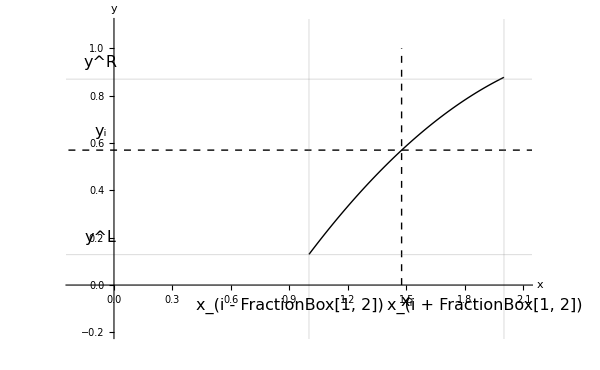

```mathematica
Subscript[ppm, visual]=Show[ppmFrames, ppmPlot, ppmLabels]
```

```mathematica
FileExport[Subscript[ppm, visual], "ppm_visual.pdf", "PDF"];
```

```mathematica
ppmlFrames = Plot[0, {x, -4, 4}, 
GridLines->{{1,2, 3}, {0.5, 1}},
PlotStyle->None, 
PlotRange->{{-0.2, 3.1}, {-0.18, 1.1}},
 TicksStyle-> Directive[Black,FontFamily -> "Times", 18], 
Ticks-> {{}, {}},
 AxesLabel->{"x", "t"}, 
AxesStyle-> Directive[Black, FontFamily-> "Times",17],
ImageSize->600
];
```

```mathematica
ppmlLabels = Graphics[{
Text[Style["t_j", FontFamily->"Times", 16], {-0.07, 0.55}],
Text[Style["t_(j + 1)", FontFamily->"Times", 16], {-0.09, 1.05}],
Text[Style["x_(i - FractionBox[1, 2])", FontFamily->"Times", 16], {1.0, -0.05}],
Text[Style["x_i", FontFamily->"Times", 16], {1.5, -0.05}],
Text[Style["x_(i + FractionBox[1, 2])", FontFamily->"Times", 16], {2.0, -0.05}],
Text[Style["x_(i + 1)", FontFamily->"Times", 16], {2.5, -0.05}],
Text[Style["x_(i + FractionBox[3, 2])", FontFamily->"Times", 16], {3, -0.05}],
PointSize[Medium],
Black,
Dashed,
Thin,
Line[{{1.5,0}, {1.5,1}}],
Line[{{2.5,0}, {2.5,1}}],
Point[{2, 1}],
PointSize[Large],
Red,
Inset[Rotate[Text[Style["a > 0",  FontFamily->"Times", 16, Bold]],45 Degree],{1.63,0.78}],
Point[{1.375, 0.5}],
Cyan,
Inset[Rotate[Text[Style["a < 0",  FontFamily->"Times", 16, Bold]],-54 Degree],{2.38,0.78}],
Point[{2.625, 0.5}]
}];
```

```mathematica
ppmlNegative = Plot[0.8x-0.6, {x, 0, 2},
PlotRange->{{0, 2}, {0.5, 1}},
PlotStyle->{Red, Thickness-> 0.005}
];
```

```mathematica
ppmlPositive = Plot[-0.8x+2.6, {x, 0, 3},
PlotRange->{{0, 3}, {0.5, 1}},
PlotStyle->{Cyan, Thickness-> 0.005}
];
```

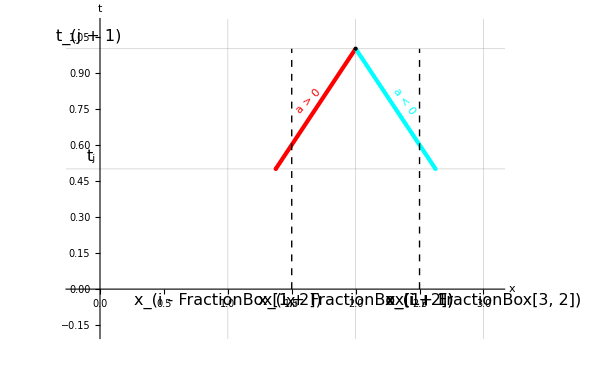

```mathematica
Subscript[ppml, visual]=Show[ppmlFrames,ppmlNegative, ppmlPositive, ppmlLabels]
```

```mathematica
FileExport[Subscript[ppml, visual], "ppml_visual.pdf", "PDF"];
```

```mathematica
flowFrames = Plot[0, {x, -4, 4}, 
GridLines->{{1,2}, {0.5, 1}},
PlotStyle->None, 
PlotRange->{{-0.2, 2.2}, {-0.18, 1.1}},
 TicksStyle-> Directive[Black,FontFamily -> "Times", 18], 
Ticks-> {{}, {}},
 AxesLabel->{"x", "t"}, 
AxesStyle-> Directive[Black, FontFamily-> "Times",17],
ImageSize->600
];
```

```mathematica
flowLabels = Graphics[{
Text[Style["t_j", FontFamily->"Times", 16], {-0.07, 0.55}],
Text[Style["t_(j + 1)", FontFamily->"Times", 16], {-0.09, 1.05}],
Text[Style["x_(i - 1)", FontFamily->"Times", 16], {0.5, -0.05}],
Text[Style["x_(i - FractionBox[1, 2])", FontFamily->"Times", 16], {1.0, -0.05}],
Text[Style["x_i", FontFamily->"Times", 16], {1.5, -0.05}],
Text[Style["x_(i + FractionBox[1, 2])", FontFamily->"Times", 16], {2.0, -0.05}],
Text[Style["a y_(i + FractionBox[1, 2])", FontFamily->"Times", 16, Bold], {2.1, 0.7}],
Text[Style["a y_(i - FractionBox[1, 2])", FontFamily->"Times", 16, Bold], {1.1, 0.7}],
Black,
Thick,
Line[{{1,0}, {1,1}}],
Line[{{2,0}, {2,1}}],
Dashed,
Thin,
Line[{{0.5,0}, {0.5,1}}],
Line[{{1.5,0}, {1.5,1}}],
PointSize[Large],
Point[{1, 0}],
Point[{1, 0.5}],
Point[{1, 1}],
Point[{2, 0}],
Point[{2, 0.5}],
Point[{2, 1}],
Point[{0.775, 0}],
Point[{0.545, 0}],
Point[{1.775, 0}],
Point[{1.545, 0}]
}];
```

```mathematica
rightFlowPlot = Show[
Plot[2.2x-3.39, {x, 1, 2}, PlotRange->{{1, 2}, {0, 1}}, PlotStyle->{Black}],
Plot[2.2x-3.9, {x, 1, 2}, PlotRange->{{1, 2}, {0, 1}}, PlotStyle->{Black}]
];
leftFlowPlot = Show[
Plot[2.2x-1.2, {x, 0, 1}, PlotRange->{{0, 1}, {0, 1}}, PlotStyle->{Black}],
Plot[2.2x-1.7, {x, 0, 1}, PlotRange->{{0, 1}, {0, 1}}, PlotStyle->{Black}]
];
```

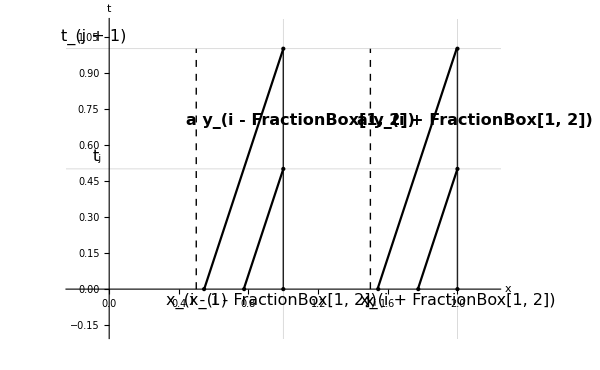

```mathematica
Subscript[flow, visual] =Show[flowFrames, flowLabels, rightFlowPlot, leftFlowPlot]
```

```mathematica
FileExport[Subscript[flow, visual], "flow_visual.pdf", "PDF"];
```